## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
safeDiv=Compile[{{num,_Real},{denom,_Real}},If[negl[denom],0,num/denom]];
magn2=Compile[{{v,_Real,1}},v.v];
magn=Compile[{{v,_Real,1}},Sqrt[magn2[v]]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
refl=Compile[{{v,_Real,1},{n,_Real,1}},2(v.n)n/magn2[n]-v];
norm=Compile[{{v,_Real,1}},v/magn[v]];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
(*ray[p0_,phat_,d_]:=p0+phat*d;*)
ray=Compile[{{p0,_Real,1},{phat,_Real,1},{d,_Real}},p0+phat*d];
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
(*x0+nx*t=0= >t=-x0/nx;*)
interY[p0_,phat_]:=Module[{t},
t=-p0[[1]]/phat[[1]];
ray[p0,phat,t]];
(*y0+ny*t=0= >t=-y0/ny;*)
interX[p0_,phat_]:=Module[{t},
t=-p0[[2]]/phat[[2]];
ray[p0,phat,t]];
```

-s (dl.dl)+(p-l1)dl==0⇒ s=(p-l1).dl/dl^2

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
closestDist[p_,l1_,l2_]:=magn[p-closestPerp[p,l1,l2]]
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
Fourth[l_]:=l[[4]];
Fifth[l_]:=l[[5]];
Sixth[l_]:=l[[6]];
Seventh[l_]:=l[[7]];
```

```mathematica
getStats[vals_]:=Module[{mean,sd,z},
mean=Mean@vals;
sd=StandardDeviation@vals;
z=safeDiv[sd,mean];
{mean,sd,z}];
```

#### Triangles

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
getSin[theCos_]:=Sqrt[1.-theCos^2];
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellGrad=Compile[{{a,_Real},{x,_Real},{y,_Real}},-{x,y a^2}];(* (x/a)^2+y^2==1 *)
ellY=Compile[{{a,_Real},{x,_Real}},Sqrt[1-(x/a)^2]];
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

CompiledFunction::cfta: Argument {x, y} at position 1 should be a rank 1 tensor of "machine-size real number"s.

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
FullSimplify[{x,y}/.Solve[{ellEqn[a,x,y]==0,ellGrad[a,x,y].{px-x,py-y}==0},{x,y}],a>0&&px∈Reals&&py∈Reals]
```

CompiledFunction::cfsa: Argument a at position 1 should be a "machine-size real number".

{{(a^2 (px^2+py √(px^2+a^2 (-1+py^2)) Abs[px]))/(px^3+a^2 px py^2),(a^2 py-√(px^2+a^2 (-1+py^2)) Abs[px])/(px^2+a^2 py^2)},{(a^2 (px^2-py √(px^2+a^2 (-1+py^2)) Abs[px]))/(px^3+a^2 px py^2),(a^2 py+√(px^2+a^2 (-1+py^2)) Abs[px])/(px^2+a^2 py^2)}}

```mathematica
Clear@ellTangents;ellTangents=Compile[{{a,_Real},{p,_Real,1}},Module[{a2,px,py,px2,px3,py2,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
px2=px*px;py2=py*py;px3=px*px2;
numFact=Sqrt[px2+a2(py2-1)]*Abs[px];
denomx=px3+a2 px py2;
denomy=px2+a2 py2;
(* NOTE: the first one is Clockwise, the 2nd one is CCW *)
{{a2(px2+py numFact)/denomx,(a2 py-numFact)/denomy},
{a2(px2-py numFact)/denomx,(a2 py+numFact)/denomy}}
]];
```

```mathematica
ellTangents[1.5,{2,2}]
```

{{1.4811,-0.158265},{-0.788787,0.850572}}

```mathematica
Module[{a=1.5,tangs,ell,gr,maxX=3,maxY=3},
ell=plotEll[a];
Manipulate[
tangs=ellTangents[a,ploc];
gr=Graphics[{PointSize@Medium,Red,Point@tangs,Thick,Blue,Line[{ploc,tangs[[1]]}],Darker@Green,Line[{ploc,tangs[[2]]}]}];
Show[{ell,gr},PlotRange->{{-maxX,maxX},{-maxY,maxY}},Frame->True],
{{ploc,{2,2}},Locator}]]
```

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{x,y},{x,y}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];
(*Clear@ellInterRayUnprot;
ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];*)
```

```mathematica
quadRootsUnprotC=Compile[{{a,_Real},{b,_Real},{c,_Real}},Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
```

```mathematica
Clear@ellInterRayUnprot;ellInterRayUnprot=Compile[{{a,_Real},{p,_Real,1},{n,_Real,1}},Module[{x,y,nx,ny,a2,c2,c1,c0,ss},
{x,y}=p;
{nx,ny}=n;
a2=a*a;
c2=nx^2+a2 ny^2;
c1=2 (nx x+a2 ny y);
c0=x^2+a2 (-1+y^2);
ss=quadRootsUnprotC[c2,c1,c0];
ray[p,n,#]&/@ss
]];
```

```mathematica
(*Module[{a=1.5,alpha=.1,p,tc,t0,n=10000},
p={1.5 Cos[alpha],Sin[alpha]};
t0=Timing[Table[ellInterRayUnprot[a,p,ellGrad[a,Sequence@@p]],{i,n}]][[1]];
tc=Timing[Table[ellInterRayUnprotC[a,p,ellGrad[a,Sequence@@p]],{i,n}]][[1]];
{t0,tc}]*)
```

```mathematica
Clear@getInterRefl;
getInterRefl=Compile[{{a,_Real},{pfrom,_Real,1},{pto,_Real,1}},Module[{norm,theRefl,pnext},
norm=ellGrad[a,pto[[1]],pto[[2]]];
theRefl=refl[pfrom-pto,norm];
pnext=ellInterRayUnprot[a,pto,theRefl][[2]];
pnext]];
```

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

#### Centroids

```mathematica
PerimeterCentroid[vtx_]:=Module[{sides,meds,per,perCentroid},
sides=triLengths@vtx;
meds=getMediansV@@vtx;
per=Total@sides;
perCentroid=Sum[meds[[i]]*sides[[i]],{i,Length@vtx}]/per;
perCentroid];
```

```mathematica
(* vtx mean, perimeter, area *)
getCentroids[vtx_]:={Mean@vtx,PerimeterCentroid@vtx,RegionCentroid[Polygon@vtx]};
```

```mathematica
Clear@getPolyCosines;
getPolyCosines[poly_]:=Module[{us},
us=MapThread[norm[#1-#2]&,{poly,RotateLeft@poly}];
MapThread[(-#1.#2)&,{us,RotateRight@us}]];
```

```mathematica
Clear@polySides;
polySides[poly_]:=MapThread[magn[#1-#2]&,{poly,RotateLeft@poly}];
```

```mathematica
getCircularity[locus_]:=Module[{rads,mean,sd},
rads=magn/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

```mathematica
(* by zscore *)
getMinCircularity[loci_]:=Module[{l,imin},
l=Select["zscore"/.Quiet@(getCircularity/@loci),NumberQ];
imin=First@First@Position[l,Min[l]];
{l[[imin]],centerNames[[imin]]}]
```

#### Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nfne[v_,n_]:=ToString@NumberForm[v,{n+2,n},NumberFormat->(Row[{#1,If[#3≠"","*10^",""],#3}]&)];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
Clear@padn;padn[n_,pads_:3]:=ToString@NumberForm[n,{pads,0},NumberPadding->{"0",""},NumberPoint->""]
```

## Ellipse Invariants

#### Constant Perimeter (Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlphaQuad[a_,x1_]:=a^2/Sqrt[a^6+a^4-a^4*x1^2+x1^2]
```

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

## triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Options[getOrbitData]={posY->False};Clear@getOrbitData;getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->{o1,"inter"/.pos,"nextInter"/.pos},
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
Clear@orbitNormals;orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit"/.orbitData,"normals"/.orbitData}
];
```

```mathematica
getAlpha[a_,t_]:=Module[{x1,ca},
x1=a * Cos[t];
ca=cosAlpha[a,a Cos[t]];
ArcCos[ca]];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals},
{orbit,normals}=orbitNormals[a,t];
getPolyCosines[orbit]];
```

## Major triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Trilinears

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(a x A+b y B+c z C)/denom];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getCircumcenterTrilin2[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
cosA=lawOfCosines[a,b,c];
cosB=lawOfCosines[b,a,c];
cosC=lawOfCosines[c,a,b];
trilinearToCartesian[orbit,{a,b,c},{cosA,cosB,cosC}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getPolyCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
```

```mathematica
getSymmedian[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMitten[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getGergonne[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagel[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpieker[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
getCentroid[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
```

#### Generate Billiard as Locus

```mathematica
getX100trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX88trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
```

## Basic Clrs and Drawing

```mathematica
ptClrs={
"ell"->Black,
"med"->Black,
"bar"->Purple,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Red,
"npc"->RGBColor[1.,0.02,0.3],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"feu"-> RGBColor[0.5,0.5,0.27],
"antifeu"->Orange,
"x88"->Cyan,
"nag"->Red,
"mit"->Lighter@Blue,
"sym"->Red,
"ger"->Pink,
"spi"->Darker@Cyan,
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,size_,where_]:=Text[Style[Subscript[txt,subscr],size],where];
```

## Poly Utils

```mathematica
Clear@polyVtx;
polyVtx[alphaT_,i_,fnVtx0_]:=Module[{a,p1,t,alpha},
(* ps={a Cos[toRad[#]],Sin[toRad[#]]}&/@("ts"/.alphaT); *)
a="a"/.alphaT;
alpha=("alphas"/.alphaT)[[i]];
t=("tsRad"/.alphaT)[[i]];
p1={a Cos[t],Sin[t]};
fnVtx0[a,p1,alpha]
];
```

```mathematica
Clear@polyError;
polyError[alphaT_,i_,fnVtx0_,fnErrorP_]:=Module[{a,alpha,poly,err},
a="a"/.alphaT;
alpha=("alphas"/.alphaT)[[i]];
poly=polyVtx[alphaT,i,fnVtx0];
err=fnErrorP[a,poly[[1]],alpha];
{"a"->a,"poly"->poly,"error"->err}];
```

```mathematica
Clear@sumPolyCosines;
sumPolyCosines[alphaT_,i_,fnVtx0_]:=Module[{poly},
(* ps={a Cos[toRad[#]],Sin[toRad[#]]}&/@("ts"/.alphaT); *)
poly=polyVtx[alphaT,i,fnVtx0];
Total@getPolyCosines[poly]
];
```

```mathematica
Clear@getP2Alpha;getP2Alpha[a_,p1_,alpha_]:=Module[{norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
(*y=-ellY[a,x1];
p1={x1,y};*)
ca=Cos[alpha];
sa=Sin[alpha];
norm=ellGrad[a,p1[[1]],p1[[2]]];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

```mathematica
Clear@plotPolyCos;
Options[plotPolyCos]={pert->.02,keep->All,cosDiv->2,clrs->{Black,Red,Green,Blue,Cyan,Magenta,Orange,Brown}};
plotPolyCos[alphaT_,fnVtx0_,OptionsPattern[]]:=Module[{ts,polys,cosPoly,theN,clrs0,clrs0k,plotData,ticksx,ticksxGrid,ticksy,keep0},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
theN=Length[polys[[1]]];
clrs0=Take[OptionValue@clrs,1+theN];
cosPoly=getPolyCosines/@polys;
keep0=Part[Range[theN],OptionValue@keep];
clrs0k=Part[clrs0,{1,Sequence@@(keep0+1)}];
ts="tsDeg"/.alphaT;
ticksx=Table[i,{i,0,Max[ts]+1,30}];
ticksxGrid=ticksx/.{180->{180,Directive[Thick,Black,Dashed,Opacity@.75]}};
ticksy=Table[i,{i,-1.5,1.5,.1}];
plotData=Transpose/@
{{ts,(Total/@cosPoly)/OptionValue@cosDiv+OptionValue@pert},
Sequence@@MapIndexed[{ts,#1+RandomReal[{-OptionValue@pert,OptionValue@pert}]}&,Transpose[Part[#,keep0]&/@cosPoly]]};
Legended[ListLinePlot[plotData,
Frame->True,FrameStyle->12,PlotStyle->clrs0k,
AspectRatio->.25,
PlotRange->{{0,360},Automatic},
FrameTicks->{{ticksy,None},{ticksx,None}},GridLines->{ticksxGrid,ticksy}, ImageSize->800,PlotLabel->Style["N="<>ToString@theN,{16,Black}]],
LineLegend[Directive[{Thick,#}]&/@clrs0k,
Style[#,16]&/@Flatten@{"Σcos"<>If[OptionValue@cosDiv≠1,"/"<>ToString[OptionValue@cosDiv],""],
("cos("<>#<>")")&/@Part[{"A","B","C","D","E","F","G"},keep0]}]]];
```

## Draw Poly

```mathematica
Clear@drawPoly;
Options[drawPoly]={drNotables->False,drSubtri->False,drLoci->False,drMedians->False,drExcentral->False,drCentroids->False,drCentroidLabels->False,drError->False,drCircs->False,drIncs->False,vtx->{1,2,3},plotAll->False};
drawPoly[polyErr_,notableLoci_,OptionsPattern[]]:=Module[{poly,a,centroids,centroidNames,lab,pnames,meds,polyTangs,polyInters,polyInterNames,tri1,notables,circs,incs,
lgt=.25,fnt=14},
poly="poly"/.polyErr;
a="a"/.polyErr;
centroids=getCentroids[poly];
centroidNames={"G_vtx","G_per","G_lam"};
lab="error: "<>nfn[N@("error"/.polyErr),3];
pnames=Take[{"A","B","C","D","E","F","G","H","I","J","K"},Length@poly];
meds=getMediansV@poly;
polyTangs=perp[ellGrad[a,#[[1]],#[[2]]]]&/@poly;
polyInters=MapThread[interRays[#1,#2,#3,#4]&,{poly,polyTangs,RotateLeft@poly,RotateLeft@polyTangs}];
polyInterNames=If[OptionValue@drExcentral,MapThread[(#1<>"'"<>#2<>"'")&,{pnames,RotateLeft@pnames}],{}];
(* *** *)
If[OptionValue@drCircs,Module[{sides,tri,cir},
circs=Table[
tri=Take[RotateLeft[poly,i-1],3];
cir=getCircumcenterTrilin[tri,RotateLeft@triLengths@tri];
(*cir=getCircumcenter@@tri;*)
{cir,magn[cir-tri[[1]]]},(* returns circumcenter and circumradius *)
{i,Length@poly}];
(*circs=Take[circs,1];*)
]];
If[OptionValue@drIncs,Module[{sides,tri,inc},
incs=Table[
tri=Take[RotateLeft[poly,i-1],3];
inc=getIncenterTrilin[tri,RotateLeft@triLengths@tri];
(*cir=getCircumcenter@@tri;*)
{inc,closestDist[inc,tri[[1]],tri[[2]]]},(* returns circumcenter and circumradius *)
{i,Length@poly}];
(*circs=Take[circs,1];*)
]];
If[OptionValue@drNotables||OptionValue@drSubtri,Module[{normals},
tri1=Part[poly,OptionValue@vtx];
normals=gettriBisectors@@tri1;
notables=getNotables[tri1,normals];
]];
gr=Graphics[{PointSize@Large,Point@poly,FaceForm@None,
{EdgeForm[{Black,Thick}],FaceForm@Gray,Opacity@.1,Polygon@poly,Black,Point@poly},
{Black,Arrowheads[Medium],MapThread[drawArrow[#1,norm[perpNeg[#2]],lgt]&,{poly,polyTangs}]},
If[OptionValue@drCentroids,{Black,MapThread[{Point@#1,If[OptionValue@drCentroidLabels,Text[Style[#2,14],#1,{0,-1.5}],{}]}&,{centroids,centroidNames}]},{}],
If[OptionValue@drExcentral,{EdgeForm@Darker@Green,Polygon@polyInters,Darker@Green,Point@polyInters,
MapThread[Text[Style[#1,fnt],#2,{-1.25,-1.25}]&,{polyInterNames,polyInters}]},{}],
{Black,MapThread[Text[Style[#1,fnt],ray[#2,norm[perp[#3]],lgt/2]]&,{pnames,poly,polyTangs}]},
If[OptionValue@drMedians,{{Dashed,Blue,Line[{#,{0,0}}]&/@polyInters},
{Blue,Point@meds,Point@{0,0}}},{}],
If[OptionValue@drCircs,{Red,{Dashed,Circle[#[[1]],#[[2]]]&/@circs},Point[First/@circs],Circle[circs[[1,1]],.05]},{}
],
If[OptionValue@drIncs,{Darker@Green,Dashed,Circle[#[[1]],#[[2]]]&/@incs,Point[First/@incs]},{}
],
If[OptionValue@drNotables,{List@@drawSomeNotables[notables,First@notableLoci],EdgeForm@None,FaceForm@Red,Opacity@.1,Polygon@tri1},{}],
If[OptionValue@drSubtri,{EdgeForm@None,FaceForm@Red,Opacity@.2,Polygon@tri1},{}]
}];
Show[{plotEll[a],gr,If[OptionValue@drLoci,Second@notableLoci,{}]},
If[OptionValue@drError,PlotLabel->lab,{}],
PlotRange->(If[OptionValue@plotAll,All,{{-2,2},{-1.5,1.5}}]),
Frame->True,FrameStyle->Medium,
AxesStyle->Directive[{Dotted,Gray}]]];
```

```mathematica
Clear@showOnePoly;
showOnePoly[alphaT_,i_,notableLoci_,fnVtx0_,fnErrorP_,opts:OptionsPattern[]]:=Module[{polyErr},
polyErr=polyError[alphaT,i,fnVtx0,fnErrorP];
drawPoly[polyErr,notableLoci,FilterRules[{opts}, Options[drawPoly]]]];
```

```mathematica
Clear@getPolyNotableLoci;
getPolyNotableLoci[alphaT_,fnVtx0_,vtx_:{1,2,3},nots_:{"inc","bar","ort"}]:=Module[{polys,normals,tris,notables},
(*{"cir","npc","mit","feu"};*)
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
polys=Append[polys,First@polys];
tris=Part[#,vtx]&/@polys;
normals=gettriBisectors@@#&/@tris;
notables=MapThread[getNotables[#1,#2]&,{tris,normals}];
{nots,ListLinePlot[Transpose[nots/.notables],PlotStyle->(nots/.ptClrs)]}
];
```

```mathematica
makeVtxLabs[vtxList_]:=StringJoin/@Map[ToString,vtxList,{2}];
```

```mathematica
Clear@manipulatePolyVtx;
manipulatePolyVtx[alphaT_,notableLociList_,fnVtx0_,fnErrorP_,vtxList_:{{1,2,3}}]:=Module[{vtxLabs,vtxMatch,lociMatch},
vtxLabs=makeVtxLabs@vtxList;
Manipulate[
vtxMatch=First@FirstPosition[vtxLabs,tri];
lociMatch=notableLociList[[vtxMatch]];
Show[
showOnePoly[alphaT,i,
lociMatch,fnVtx0,fnErrorP,
drNotables->drNotables0,drSubtri->drSubtri0,drLoci->drLoci0,
drExcentral->drExcentral0,drCentroids->drCentroids0,drCentroidLabels->drCentroidLabels0,drCircs->drCircs0,
drIncs->drIncs0,plotAll->plotAll0,
vtx->vtxList[[vtxMatch]]],ImageSize->Large],
{{i,1},1,Length["alphas"/.alphaT],1,Appearance->"Labeled"},
{{drExcentral0,False,"excentral"},{True,False}},
{{drSubtri0,False,"subtri"},{True,False}},
{{drNotables0,True,"notables"},{True,False}},
{{drLoci0,True,"loci"},{True,False}},
{{drCentroids0,True,"centroids"},{True,False}},
{{drCentroidLabels0,False,"centroidLabels"},{True,False}},
{{drCircs0,False,"circs"},{True,False}},
{{drIncs0,False,"incs"},{True,False}},
{{tri,vtxLabs[[1]]},vtxLabs},
{{plotAll0,False,"plotAll"},{True,False}},SaveDefinitions->True]];
```

```mathematica
Clear@showOneLocusVtx;
Options[showOneLocusVtx]={filling->None,fillingStyle->{Opacity@.1},plotAll->False};
showOneLocusVtx[a_,i_,lociList_,vtxList_,vtx_,OptionsPattern[]]:=Module[{vtxLabs},
vtxLabs=makeVtxLabs@vtxList;
Show[{plotEll[a],
ListLinePlot[
MapIndexed[If[vtx=="all"||vtx==#1,Legended[lociList[[First@#2,i]],vtxLabs[[First@#2]]],{{0,0}}]&,vtxLabs],
Filling->(OptionValue@filling),FillingStyle->(OptionValue@fillingStyle),PlotStyle->Thick
(*PlotStyle->{Blue,Red,Darker@Green}*)]},Frame->True,FrameStyle->Medium,PlotRange->(If[OptionValue@plotAll,All,{{-2,2},{1,1}}]),
PlotLabel->Style[centerNames[[i]]<>", a/b="<>nfn[a,2],{Black,16}],ImageSize->Large]];
```

## Numerically Calculate Exit Angle: α

```mathematica
Clear@gradDescPentErr;gradDescPentErr[a_,p1_,alpha0_,debug_:False]:=Module[{grad,dalpha=.0001,alpha,alphaSav,error=1,maxError=10^-6,eps=.001,it,itMax=1000,pentErr=1},
alpha=alpha0;
it=1;
While[error>maxError&&it<itMax,
it++;
pentErr=pentErrorP[a,p1,alpha];
grad=(pentErrorP[a,p1,alpha+dalpha]-pentErr)/dalpha;
alphaSav=alpha;
alpha=alpha-eps grad;
error=Abs[alpha-alphaSav];
If[debug&&Mod[it,100]==0,Print["it=",it,", error=",error]];
];
{it,error,alpha,pentErr}];
```

```mathematica
Clear@getPolyAlphaTOneQuarter;
getPolyAlphaTOneQuarter[errFn_,a_,alpha0_,degStep_:10,verbose_]:=Module[{lastAlpha,tRad,min,tab,ts,alphas,p1},
lastAlpha=alpha0;
tab=Table[
tRad=toRad[tDeg];
p1={a Cos[tRad],Sin[tRad]};
min=Quiet@FindMinimum[errFn[a,p1,alpha],{alpha,lastAlpha},
Method->"PrincipalAxis"(*,WorkingPrecision->40*)];
lastAlpha=(alpha/.min[[2]]);
(*min=gradDescPentErr[a,p1,lastAlpha];*)
(*lastAlpha=min[[3]];*)
If[verbose,Print["t=",tDeg,"; min=",min]];
{tDeg,tRad,lastAlpha,min},
(* takes advantage of 4-arc symmetry *)
{tDeg,0,90,degStep}];
{
"a"->a,
"tsDeg"->First/@tab,
"tsRad"->Second/@tab,
"alphas"->Third/@tab,
"mins"->(#[[4]]&/@tab)
}];
```

#### Takes Advantage of 4-arc alpha symmetry (only computes fn from 0 to 90)

```mathematica
Clear@doubleList;doubleList[vs_]:=Join[vs,Rest[Reverse@vs]];
Clear@quadrupleList;quadrupleList[vs_]:=Most[doubleList@doubleList@vs];
```

```mathematica
Clear@quadrupleT;
quadrupleT[theT_]:=Module[{degStep,radStep},
degStep=("tsDeg"/.theT)[[2]]-("tsDeg"/.theT)[[1]];
radStep=("tsRad"/.theT)[[2]]-("tsRad"/.theT)[[1]];
{
"a"->("a"/.theT),
"tsDeg"->Range[0,360-degStep,degStep],
"tsRad"->Range[0,2π-radStep,radStep],
"alphas"->quadrupleList["alphas"/.theT],
"mins"->quadrupleList["mins"/.theT]
}];
```

```mathematica
Clear@getPolyAlphaT;
getPolyAlphaT[errFn_,a_,startAlpha_,degStep_,verbose_]:=Module[{theT},
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaTOneQuarter[errFn,a,startAlpha,degStep,verbose];
theT=quadrupleT@theT;
theT];
```

```mathematica
Clear@calcAlphaT;
calcAlphaT[doCalc_(*False for load*),errFn_,fname_,a_,startAlpha_,degStep_,verbose_:True]:=Module[{theT},
If[doCalc,
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaT[errFn,a,startAlpha,degStep,verbose];
Print["saving: ",Length["alphas"/.theT]," records to",fname];
Save[fname,theT];
theT,
theT=Get[fname];
Print["loaded: ",Length["alphas"/.theT]," records from",fname];
theT]];
```

## Numerically Calculate α Using Caustics

```mathematica
Clear@getOneCosAlphaCaustic;
getOneCosAlphaCaustic[a_,p1_,acaustic_,bcaustic_]:=Module[{tangs,n},
tangs=bcaustic*ellTangents[acaustic/bcaustic,p1/bcaustic];
n=norm[ellGrad[a,Sequence@@p1]];
(* 2nd tangent is clockwise, but it doesn't matter as the normal is bisected *)
n.norm[(tangs[[1]]-p1)]];
```

#### This may take some time for high-order N-odd nonagon

```mathematica
Clear@getAlpha0;
getAlpha0[a_,errCausticFn_,x1guess_]:=Module[{min,c2,acaustic,bcaustic,p1,p2,tangs},
min=Quiet@FindMinimum[errCausticFn[a,x1],{x1,x1guess},Method->"PrincipalAxis"];
c2=a^2-1;(* b=1 *)
acaustic=-(x1/.Second[min]);
(*Subscript[a, caustic]^2-Subscript[b, caustic]^2==c^2*)
bcaustic=Sqrt[acaustic^2-c2];
tangs=bcaustic*ellTangents[acaustic/bcaustic,{a/bcaustic,0}];
p1={a,0};
p2=ellInterRayUnprot[a,p1,tangs[[2]]-p1][[2]];
{acaustic,bcaustic,tangs,p1,p2,min}];
```

```mathematica
Clear@getCosAlphasCaustic;
getCosAlphasCaustic[a_,acaustic_,bcaustic_,step_:1]:=Module[{tDegs,tRad,cossa},
tDegs=Range[0,90,1];
cossa=(tRad=toRad[#];
getOneCosAlphaCaustic[a,{a Cos[tRad],Sin[tRad]},
acaustic,bcaustic])&/@tDegs;
cossa];
```

```mathematica
Clear@getPolyAlphaCausticTOneQuarter;
getPolyAlphaCausticTOneQuarter[errCausticFn_,a_,degStep_:10,verbose_]:=Module[{tsDeg,tsRad,alphas,cosAlphas,acaustic,bcaustic,min},
tsDeg=Range[0,359,degStep];
tsRad=toRad/@tsDeg;
{acaustic,bcaustic,min}=Part[getAlpha0[a,errCausticFn,-a+.1],{1,2,6}];
cosAlphas=getCosAlphasCaustic[a,acaustic,bcaustic];
alphas=ArcCos/@cosAlphas;
{
"a"->a,
"tsDeg"->tsDeg,
"tsRad"->tsRad,
"alphas"->alphas,
"min"->min
}];
```

```mathematica
Clear@getPolyAlphaCausticT;
getPolyAlphaCausticT[errCausticFn_,a_,degStep_,verbose_]:=Module[{theT},
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaCausticTOneQuarter[errCausticFn,a,degStep,verbose];
theT=quadrupleT[theT,False];
theT];
```

```mathematica
Clear@calcAlphaCausticT;
calcAlphaCausticT[doCalc_(*False for load*),errCausticFn_,fname_,a_,degStep_,verbose_:True]:=Module[{theT},
If[doCalc,
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaCausticT[errCausticFn,a,degStep,verbose];
Print["saving: ",Length["alphas"/.theT]," records to",fname];
Save[fname,theT];
theT,
theT=Get[fname];
Print["loaded: ",Length["alphas"/.theT]," records from",fname];
theT]];
```

## Tri (Simulate AlphaT)

```mathematica
Clear@getEllVtx0;(* not for error purposes *)
getEllVtx0[a_,p1_,alpha_]:={p1};
triErrorP[a_,p1_,alpha_]:=0;
```

```mathematica
getEllAlphaT[a_]:=Module[{tsDeg,tsRad,alphas},
tsDeg=Range[360]-1;
tsRad=toRad/@tsDeg;
alphas=ConstantArray[0,Length@tsRad];
{"a"->a,"tsDeg"->tsDeg,
"tsRad"->tsRad,
"alphas"->alphas}];
```

```mathematica
ellAlphaT15=getEllAlphaT[1.5];
(*Save["data/ellAlphaT_a15.m",ellAlphaT15];*)
```

```mathematica
getTriAlphaT[a_]:=Module[{tsDeg,tsRad,alphas},
tsDeg=Range[360]-1;
tsRad=toRad/@tsDeg;
alphas=getAlpha[a,#]&/@tsRad;
{"a"->a,"tsDeg"->tsDeg,
"tsRad"->tsRad,
"alphas"->alphas}];
```

```mathematica
triAlphaT15=getTriAlphaT[1.5];
(*Save["data/triAlphaT_a15.m",triAlphaT15];*)
```

```mathematica
Clear@getTriVtx0;(* not for error purposes *)
getTriVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
{p1,p2,p2Neg}];
```

## Quadrangle

```mathematica
Clear@getQuadVtx0;(* not for error purposes *)
getQuadVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
{p1,p2,p3,p2Neg}];
```

```mathematica
doQuadAlphaT15=True;Clear@quadAlphaT15;
quadAlphaT15=calcAlphaT[doQuadAlphaT15,quadErrorP,"data/quadAlphaT_a15.m",1.5,.794,1,False];
```

FindMinimum::nrnum: The function value quadErrorP[1.5, {1.5, 0.}, 0.794] is not a real number at {alpha} = {0.794}.

General::stop: Further output of FindMinimum :: nrnum will be suppressed during this calculation.

ReplaceAll::reps: {alpha, 0.794} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

saving: 360 records todata/quadAlphaT_a15.m

## Pentagon

```mathematica
Clear@getPentVtx0;(* not for error purposes *)
getPentVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p3Neg=getInterRefl[a,p1,p2Neg];
{p1,p2,p3,p3Neg,p2Neg}];
```

#### Pentagon Exit Angle Table

```mathematica
doPentAlphaT125=False;Clear@pentAlphaT125;
pentAlphaT125=calcAlphaT[doPentAlphaT125,Function[x,0],"data/pentAlphaT_a125.m",1.25,.86,10,False];
```

loaded: 36 records fromdata/pentAlphaT_a125.m

```mathematica
doPentAlphaT15=False;Clear@pentAlphaT15;
pentAlphaT15=calcAlphaT[doPentAlphaT15,Function[x,0],"data/pentAlphaT_a15.m",1.5,.794,1,True];
```

loaded: 360 records fromdata/pentAlphaT_a15.m

```mathematica
doPentAlphaT20=False;Clear@pentAlphaT20;
pentAlphaT20=calcAlphaT[doPentAlphaT20,Function[x,0],"data/pentAlphaT_a20.m",2.0,.69,10,False];
```

loaded: 36 records fromdata/pentAlphaT_a20.m

```mathematica
doPentAlphaT30=False;Clear@pentAlphaT30;
pentAlphaT30=calcAlphaT[doPentAlphaT30,Function[x,0],"data/pentAlphaT_a30.m",3.0,.55,5,False];
```

loaded: 72 records fromdata/pentAlphaT_a30.m

```mathematica
reportErrorsAlphaT[alphaT_]:=Module[{errors},
errors=First/@("mins"/.alphaT);
{Length@errors,Mean@errors,Max@errors,Min@errors}]
```

```mathematica
reportErrorsAlphaT/@{pentAlphaT125,pentAlphaT15,pentAlphaT20,pentAlphaT30}//ColumnForm
```

{36,3.13753×10^-13,1.41451×10^-12,7.08896×10^-16}
{360,3.23944×10^-6,0.000291471,6.07529×10^-16}
{36,3.39754×10^-13,2.76421×10^-12,2.16162×10^-15}
{72,4.05773×10^-7,5.79672×10^-6,2.0542×10^-15}

## Hexagon

```mathematica
Clear@getHexVtx0;(* not for error purposes *)
getHexVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p4,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
{p1,p2,p3,p4,p3Neg,p2Neg}];
```

#### Hexagon Exit Angle Table

```mathematica
doHexAlphaT15=False;Clear@hexAlphaT15;
hexAlphaT15=calcAlphaT[doHexAlphaT15,Function[x,0],"data/hexAlphaT_a15.m",1.5,.9273,1,True];
```

loaded: 360 records fromdata/hexAlphaT_a15.m

## Sum of Cosine Graphs

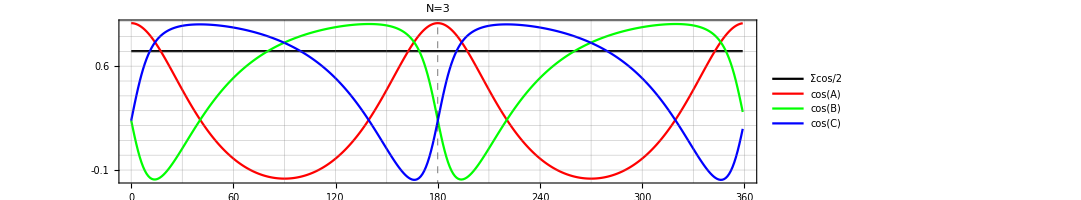
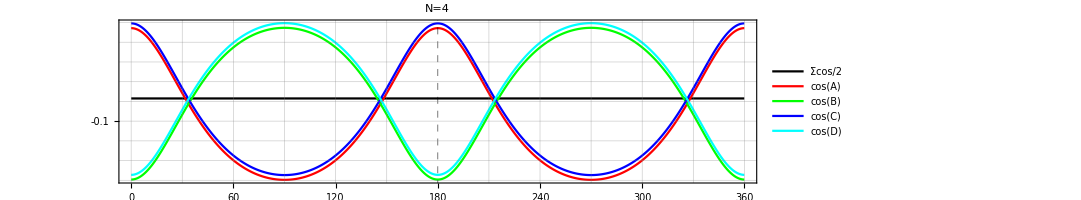
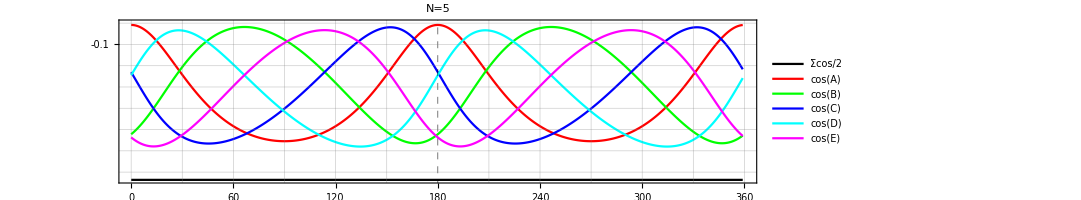
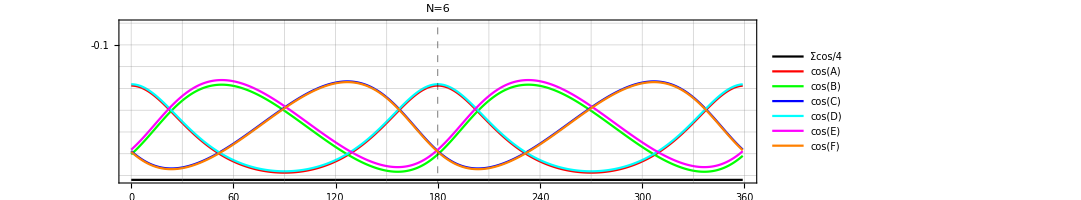
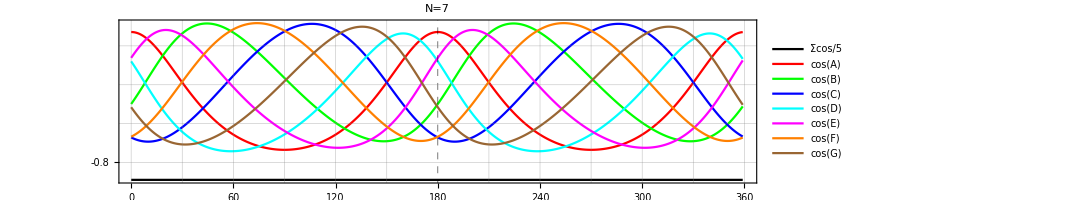

## Plot C1, C2, C3

```mathematica
getMaxVtx[n_]:=Switch[n,
3,1,
  4,2,
5,3,
  6,2,
7,4,
  8,6,
9,5];
```

```mathematica
vtxList0={{1,2,3},{1,2,4},{1,3,5},{1,2,5},{1,2,6},{1,4,7}};
```

```mathematica
Clear@getPolyCos;getPolyCos[alphaT_,fnVtx0_,vtxList_:vtxList0]:=Module[{polys,coss,cosSum,poly0,n,inter,intAngSum,maxVtx},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
poly0=First@polys;
n=Length@poly0;
coss=getPolyCosines/@polys;
cosSum=Total[First@coss];
intAngSum=(n-2)π;
maxVtx=getMaxVtx[n];
Table[Part[#,vtxList[[i]]]&/@coss,{i,maxVtx}]
];
```

```mathematica
Clear@getSubtriPer;getSubtriPer[alphaT_,fnVtx0_,vtxList_:vtxList0]:=Module[{polys,coss,cosSum,poly0,n,inter,intAngSum,maxVtx},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
poly0=First@polys;
n=Length@poly0;
maxVtx=maxVtx=getMaxVtx[n];
Table[getStats[triPer[Part[#,vtxList[[i]]]]&/@polys],{i,maxVtx}]];
Clear@getSubtriArea;getSubtriArea[alphaT_,fnVtx0_,vtxList_:vtxList0]:=Module[{polys,coss,cosSum,poly0,n,inter,intAngSum,maxVtx},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
poly0=First@polys;
n=Length@poly0;
maxVtx=maxVtx=getMaxVtx[n];
Table[getStats[Area[Polygon[Part[#,vtxList[[i]]]]]&/@polys],{i,maxVtx}]]
```

```mathematica
Clear@plotCS;plotCS[alphaT_,fnVtx0_]:=Module[{cs,poly,coss,n,clrs={Red,Darker@Green,Blue,Magenta,Cyan,Orange}},
coss=getPolyCos[alphaT,fnVtx0];
n=Length[coss];
Manipulate[
cs=Graphics3D[{Thick,PointSize@Large,
MapThread[{#1,Line[coss[[#2]]],Point[coss[[#2]][[i]]]}&,{Take[clrs,n],Range[n]}]},
SphericalRegion->True, Axes->True,AxesLabel->(Style[#,{Black,14}]&/@{"c1","c2","c3"}),ImageSize->Medium];
poly=Show[showOnePoly[alphaT,i,{},fnVtx0,Function[x,0],drSubhex->True,plotAll->False,vtx->{1,2,3}],ImageSize->Medium];
Grid[{{poly,cs}}],{i,1,Length[First@coss],1,Appearance->"Labeled"},SaveDefinitions->True]]
```

```mathematica
Clear@plotCSgr;plotCSgr[alphaT_,fnVtx0_,lab_:""]:=Module[{cs,poly,coss,n,clrs={Red,Darker@Green,Blue,Magenta,Cyan}},
coss=getPolyCos[alphaT,fnVtx0];
n=Length[coss];
cs=Graphics3D[{Thick,PointSize@Large,
MapThread[{#1,Line[coss[[#2]]],Point[coss[[#2]][[1]]]}&,{Take[clrs,n],Range[n]}]},
SphericalRegion->True,Axes->True,AxesLabel->(Style[#,{Black,14}]&/@{"c1","c2","c3"}),ImageSize->Large];
cs];
```

## Config Tri

```mathematica
plotCS[triAlphaT15,getTriVtx0]
```

## Config Quad

```mathematica
Clear@getQuadVtx;
getQuadVtx[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p3Neg=getInterRefl[a,p1,p2Neg];
{p2,p2Neg,p3,p3Neg}];
Clear@getQuadVtx0;(* not for error purposes *)
getQuadVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
{p1,p2,p3,p2Neg}];
```

```mathematica
Clear@quadAlphaT15;
quadAlphaT15=calcAlphaT[False,Function[x,0],"data/quadAlphaT_a15.m",1.5,.794,1,False];
```

loaded: 360 records fromdata/quadAlphaT_a15.m

```mathematica
plotCS[quadAlphaT15,getQuadVtx0]
```

## Config Pent

```mathematica
plotCS[pentAlphaT15,getPentVtx0]
```

```mathematica
(*CloudDeploy[plotCSgr[pentAlphaT15,getPentVtx0],Permissions->"Public"]*)
```

## Config Hex

```mathematica
plotCS[hexAlphaT15,getHexVtx0]
```

```mathematica
Show[{plotCSgr[hexAlphaT15,getHexVtx0],plotCSgr[triAlphaT15,getTriVtx0]},ViewPoint->{100,100,100}]
```

-Graphics3D-

```mathematica
(*CloudDeploy[plotCSgr[hexAlphaT15,getHexVtx0]]*)
```

## Heptagon

```mathematica
Clear@getHeptVtx0;(* not for error purposes *)
getHeptVtx0[a_,p1_,alpha_]:=Module[{p2,p3,p4,p2Neg,p3Neg,p4Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
{p1,p2,p3,p4,p4Neg,p3Neg,p2Neg}];
```

#### Heptagon Exit Angle Table

```mathematica
Clear@heptAlphaT15;
heptAlphaT15=calcAlphaCausticT[False(*False for load*),
Function[x,0],"data/heptAlphaCausticT_a15.m",1.5,1];
```

loaded: 360 records fromdata/heptAlphaCausticT_a15.m

```mathematica
plotCS[heptAlphaT15,getHeptVtx0]
```

```mathematica
(*CloudDeploy[plotCSgr[heptAlphaT15,getHeptVtx0]]*)
```

## Octagon

```mathematica
Clear@getOctVtx0;(* not for error purposes *)
getOctVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p4,p5,p3Neg,p4Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p5=getInterRefl[a,p3,p4];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
{p1,p2,p3,p4,p5,p4Neg,p3Neg,p2Neg}];
```

```mathematica
doOctAlphaT15=False;Clear@octAlphaT15;
octAlphaT15=calcAlphaT[doOctAlphaT15,Function[x,0],"data/octAlphaT_a15.m",1.5,.9273,1,True];
```

loaded: 360 records fromdata/octAlphaT_a15.m

```mathematica
plotCS[octAlphaT15,getOctVtx0]
```

```mathematica
Show[{
plotCSgr[octAlphaT15,getOctVtx0],
plotCSgr[hexAlphaT15,getHexVtx0],
plotCSgr[triAlphaT15,getTriVtx0]},ViewPoint->{1000,1000,1000},SphericalRegion->True]
```

-Graphics3D-

```mathematica
(*CloudDeploy[%,Permissions->"Public"]*)
```

## Nonagon

```mathematica
Clear@getNonaVtx0;(* not for error purposes *)
getNonaVtx0[a_,p1_,alpha_]:=Module[{p2,p3,p4,p5,p2Neg,p3Neg,p4Neg,p5Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p5=getInterRefl[a,p3,p4];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
p5Neg=getInterRefl[a,p3Neg,p4Neg];
{p1,p2,p3,p4,p5,p5Neg,p4Neg,p3Neg,p2Neg}];
```

```mathematica
Clear@nonaAlphaT15;
nonaAlphaT15=calcAlphaCausticT[False(*False for load*),
Function[x,0],"data/nonaAlphaCausticT_a15.m",1.5,1];
```

loaded: 360 records fromdata/nonaAlphaCausticT_a15.m

#### Nonagon Exit Angle Table

```mathematica
plotCS[nonaAlphaT15,getNonaVtx0]
```

```mathematica
(*CloudDeploy[plotCSgr[heptAlphaT15,getHeptVtx0]]*)
```

## Show Projections

#### Planar : 3, 4, 6

```mathematica
proj3d[vx_,vy_,p_]:={vx.p,vy.p};
```

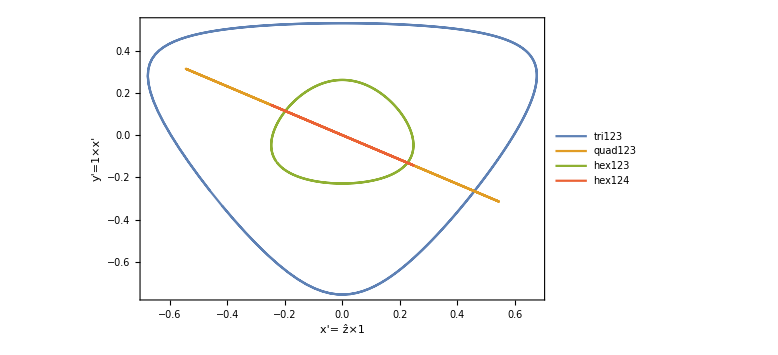

```mathematica
Module[{vnorm={1,1,1},zhat={0,0,1},vx,vy,triCos,quadCos,hexCos,
tri123,quad123,hex123,hex124},
vx=norm[zhat×vnorm];
vy=norm[vnorm×vx];
triCos=getPolyCos[triAlphaT15,getTriVtx0];
quadCos=getPolyCos[quadAlphaT15,getQuadVtx0];
hexCos=getPolyCos[hexAlphaT15,getHexVtx0];
tri123=proj3d[vx,vy,#]&/@(First@triCos);
quad123=proj3d[vx,vy,#]&/@(First@quadCos);
hex123=proj3d[vx,vy,#]&/@(First@hexCos);
hex124=proj3d[vx,vy,#]&/@(Second@hexCos);
ListLinePlot[{
Legended[tri123,"tri123"],
Legended[quad123,"quad123"],
Legended[hex123,"hex123"],
Legended[hex124,"hex124"]},
PlotStyle->Thick,
Frame->True,
FrameLabel->(Style[#,16]&/@{"x'= ẑ×1","y'=1×x'"}),
FrameStyle->Directive[Black,Medium],ImageSize->Large]]
```

#### Non-Planar : 5, 7

```mathematica
Module[{vnorm={1,1,1},vnormRot,zhat={0,0,1},vx,vy,pentCos,heptCos,
pent123,pent124,pent125,hept123,hept124,hept125,hept135,
maxX=.5,maxY=.5},
pentCos=getPolyCos[pentAlphaT15,getPentVtx0];
heptCos=getPolyCos[heptAlphaT15,getHeptVtx0];
Manipulate[
vnormRot=RotationMatrix[toRad@thy,{0,1,0}].RotationMatrix[toRad@thx,{1,0,0}].vnorm;
vx=norm[zhat×vnormRot];
vy=norm[vnormRot×vx];
pent123=proj3d[vx,vy,#]&/@(First@pentCos);
pent124=proj3d[vx,vy,#]&/@(Second@pentCos);
pent125=proj3d[vx,vy,#]&/@(Third@pentCos);
hept123=proj3d[vx,vy,#]&/@(First@heptCos);
hept124=proj3d[vx,vy,#]&/@(Second@heptCos);
hept125=proj3d[vx,vy,#]&/@(Third@heptCos);
hept135=proj3d[vx,vy,#]&/@(Fourth@heptCos);
ListLinePlot[{
Legended[pent123,"pent123"],
Legended[pent124,"pent124"],
Legended[pent125,"pent125"],
Legended[hept123,"hept123"],
Legended[hept124,"hept124"],
Legended[hept125,"hept125"],
Legended[hept125,"hept135"]},
PlotStyle->({Thick,#}&/@{Thick,Thick,Thick,Dashed,Dashed,Dashed,Dashed}),
PlotRange->{{-maxX,maxX},{-maxY,maxY}},
Frame->True,
FrameLabel->(Style[#,16]&/@{"x'= ẑ×1","y'=1×x'"}),
FrameStyle->Directive[Black,Medium],ImageSize->Large],
{{thx,0},-90,90,.1,Appearance->"Labeled"},
{{thy,0},-90,90,.1,Appearance->"Labeled"}]]
```

## Subtriangle Perimeters: Perimeter, Area

```mathematica
MapThread[getSubtriPer[#1,#2]&,
Transpose@{{triAlphaT15,getTriVtx0},
{quadAlphaT15,getQuadVtx0},
{pentAlphaT15,getPentVtx0},
{hexAlphaT15,getHexVtx0},
{heptAlphaT15,getHeptVtx0},
{octAlphaT15,getOctVtx0},
{nonaAlphaT15,getNonaVtx0}}]//Map[First,#,{2}]&//ColumnForm
```

{6.73751}
{6.13061,6.31843}
{5.33357,6.40123,6.40123}
{4.68415,6.00921}
{4.16186,5.52299,6.48093,6.09415}
{3.73586,5.06384,6.12505,5.85501,5.91353,6.54914}
{3.3834,4.65711,5.73167,5.53901,5.89151}

#### The Only N which conserves perimeter is N = 4

```mathematica
MapThread[getSubtriPer[#1,#2]&,
Transpose@{{triAlphaT15,getTriVtx0},
{quadAlphaT15,getQuadVtx0},
{pentAlphaT15,getPentVtx0},
{hexAlphaT15,getHexVtx0},
{heptAlphaT15,getHeptVtx0},
{octAlphaT15,getOctVtx0},
{nonaAlphaT15,getNonaVtx0}}]//Map[Third,#,{2}]&//ColumnForm
```

{4.90987×10^-15}
{0.057532,0.0505757}
{0.1205,0.0304464,0.0304464}
{0.162287,0.0630487}
{0.189658,0.0999113,0.0277777,0.0560231}
{0.208198,0.130868,0.0574037,0.0740939,0.0728002,0.0210047}
{0.221233,0.155431,0.0856958,0.0973506,0.0723844}

#### No Subtri areas remain constant

```mathematica
MapThread[getSubtriArea[#1,#2]&,
Transpose@{
{triAlphaT15,getTriVtx0},
{quadAlphaT15,getQuadVtx0},
{pentAlphaT15,getPentVtx0},
{hexAlphaT15,getHexVtx0},
{heptAlphaT15,getHeptVtx0},
{octAlphaT15,getOctVtx0},
{nonaAlphaT15,getNonaVtx0}}]//ColumnForm
```

{{1.75782,0.0326232,0.0185589}}
{{1.44288,0.0408453,0.0283081},{1.44288,0.0408453,0.0283081}}
{{0.940864,0.103295,0.109788},{1.58423,0.169383,0.106918},{1.58423,0.169383,0.106918}}
{{0.629233,0.120441,0.191409},{1.29311,0.12046,0.0931553}}
{{0.436902,0.106983,0.244867},{0.980176,0.0854016,0.0871289},{1.7718,0.0427433,0.0241242},{1.2468,0.15502,0.124334}}
{{0.31358,0.0879312,0.280411},{0.739537,0.0879312,0.1189},{1.47936,0.0146629,0.00991164},{1.0679,0.123492,0.11564},{1.0679,0.123492,0.11564},{1.79294,0.0879312,0.0490429}}
{{0.23157,0.0706114,0.304924},{0.565608,0.0902859,0.159626},{1.19564,0.0455814,0.0381231},{0.875814,0.0893603,0.102031},{1.00806,0.13176,0.130706}}